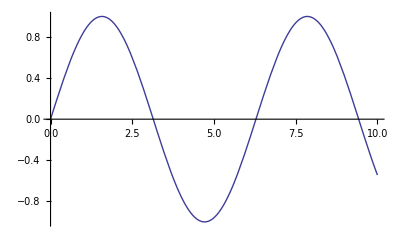

```mathematica
Plot[Sin[x],{x,0,10}]
```

```mathematica
d=1.6*10^-5
```

0.000016

```mathematica
N[Pi]
```

3.14159

```mathematica
l=632.8*10^-9
```

6.328×10^-7

```mathematica
u[t_]:=1/n^2(Sin[n*Pi*d *Sin[t]/l]/Sin[Pi*d *Sin[t]/l])^2
```

```mathematica
n=5
```

5

1000

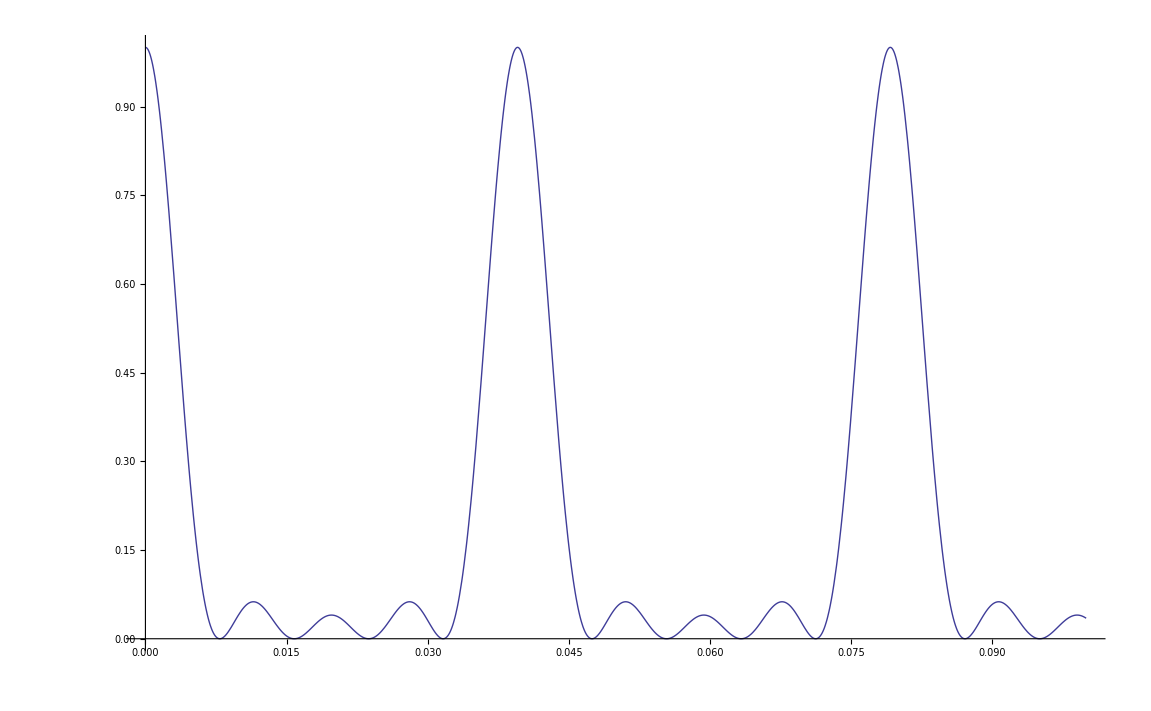

```mathematica
Plot[u[z],{z,0,0.1},PlotRange->Full]
```

```mathematica
d/l
```

15.8028

```mathematica
L=0.0005
```

0.0005

```mathematica
u[t_]:=1/n^2(Sin[Pi*L*Sin[t]/l]/Sin[Pi*L/n *Sin[t]/l])^2
```

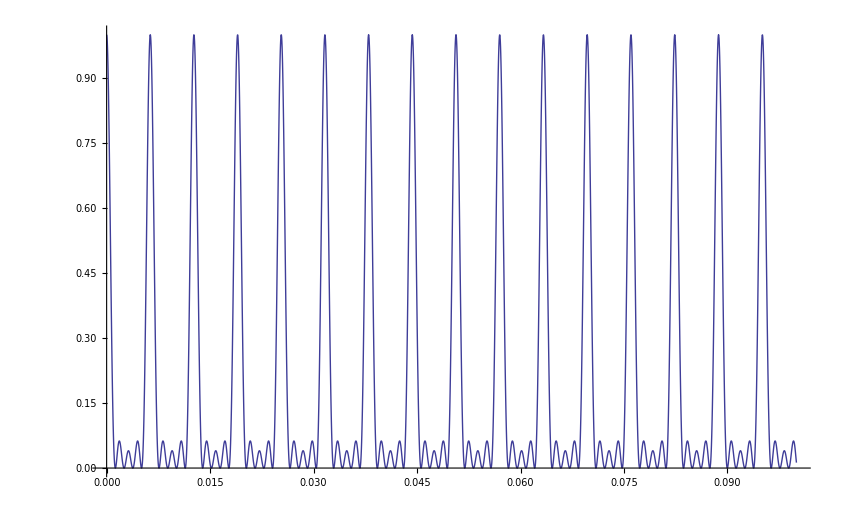

```mathematica
Plot[u[x],{x,0,0.1},PlotRange->Full]
```

```mathematica
g[t_]:=(Sin[Pi*L*Sin[t]/l]/(Pi*L*Sin[t]/l))^2
```

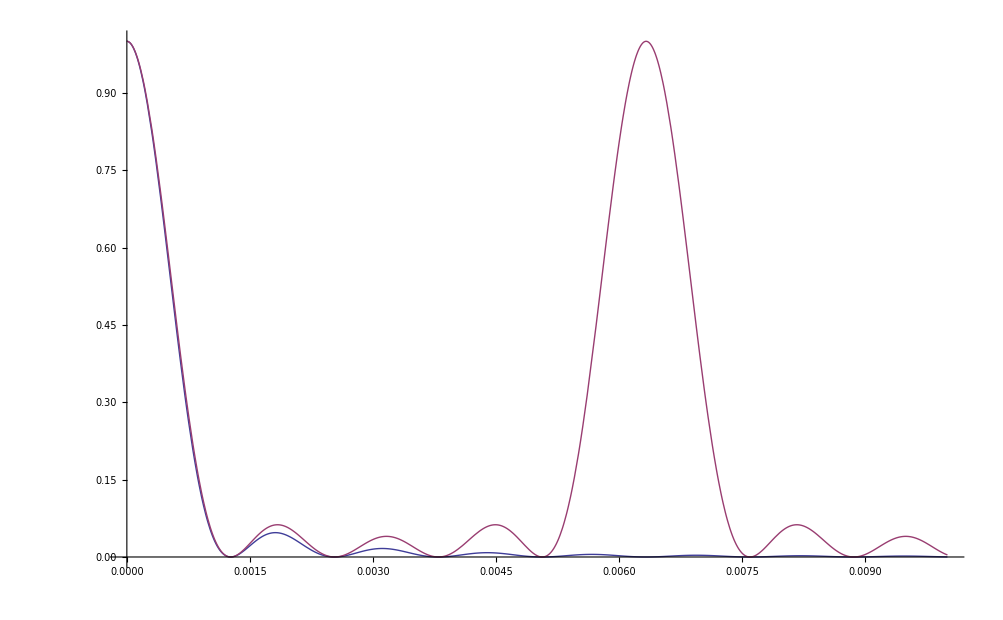

```mathematica
Plot[{g[x],u[x]},{x,0,0.01},PlotRange->Full]
```

```mathematica
int[t_]:=(Sin[d*Pi*Sin[t]/l]/(d*Pi*Sin[t]/l))^2*(Cos[h*Pi*Sin[t]/l])^2
```

```mathematica
d=0.000005
h=0.000035
```

5.×10^-6

0.000035

```mathematica
d=0.000035
```

0.000035

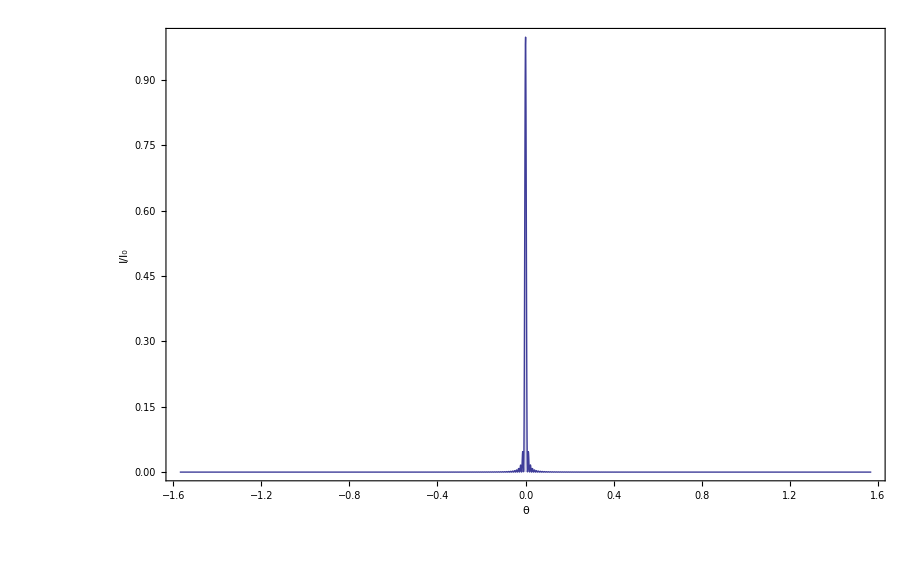

```mathematica
Plot[int[r],{r,-Pi/2,Pi/2},PlotRange->Full,FrameLabel-> {"θ","I/I_0"},Filling->Axis,Frame->True,TextStyle->{FontFamiy->"Helvetica",FontSize->25}]
```

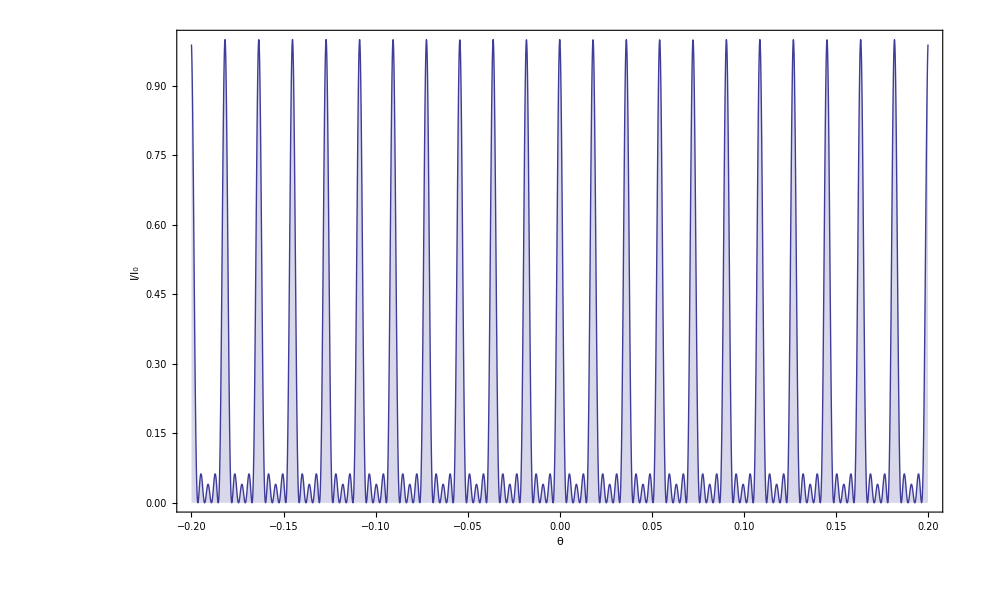

```mathematica
Plot[u[r],{r,-0.2,0.2},PlotRange->Full,FrameLabel-> {"θ","I/I_0"},Filling->Axis,Frame->True,TextStyle->{FontFamiy->"Helvetica",FontSize->25}]
```

```mathematica
u[t_]:=1/n^2(Sin[n*Pi*d *Sin[t]/l]/Sin[Pi*d *Sin[t]/l])^2
```

```mathematica
Plot[(Sin[Pi*d *Sin[r]/l]/(Pi*d *Sin[r]/l))^2,{r,-0.1,0.1},PlotRange->Full,FrameLabel-> {"θ","I/I_0"},Filling->Axis,Frame->True,TextStyle->{FontFamiy->"Helvetica",FontSize->25}]
```

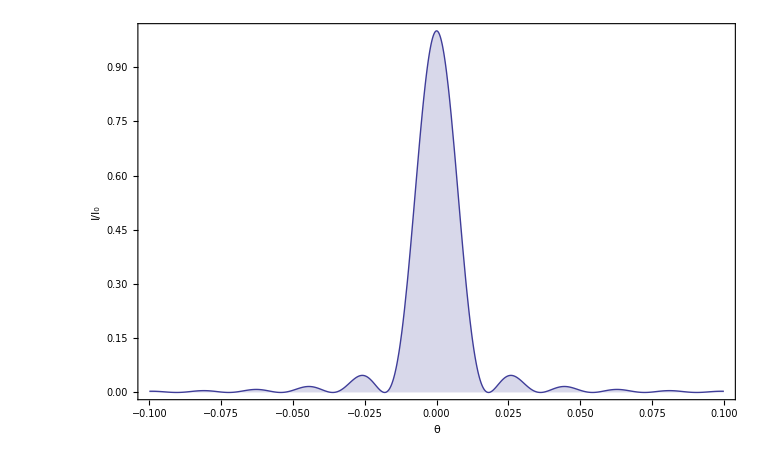
```mathematica
-Graphics-2dplo
```

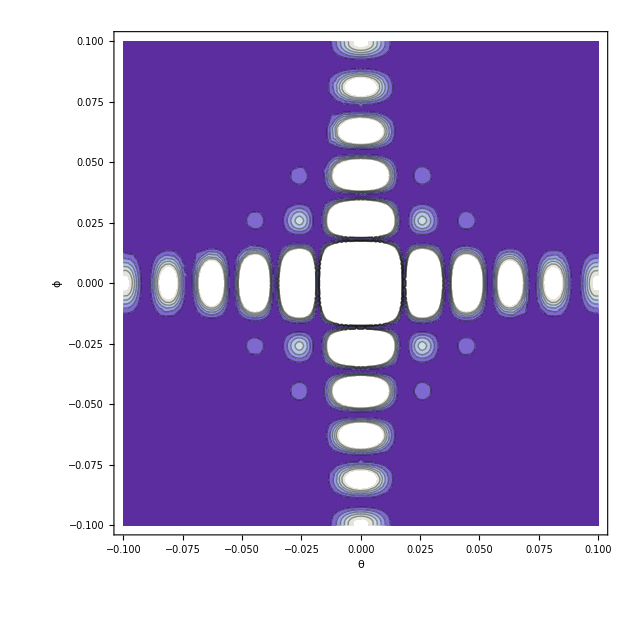

```mathematica
ContourPlot[(Sin[Pi*d *Sin[r]/l]/(Pi*d *Sin[r]/l))^2(Sin[Pi*d *Sin[q]/l]/(Pi*d *Sin[q]/l))^2,{r,-0.1,0.1},{q,-0.1,0.1},FrameLabel-> {"θ","ϕ"},Frame->True,TextStyle->{FontFamiy->"Helvetica",FontSize->25}]
```

```mathematica
irr[f_]:=(BesselJ[1,2*Pi*R*Sin[f]/l]/(Pi*R*Sin[f]/l))^2
```

```mathematica
R=2.014264959771028*^-6
```

2.01426×10^-6

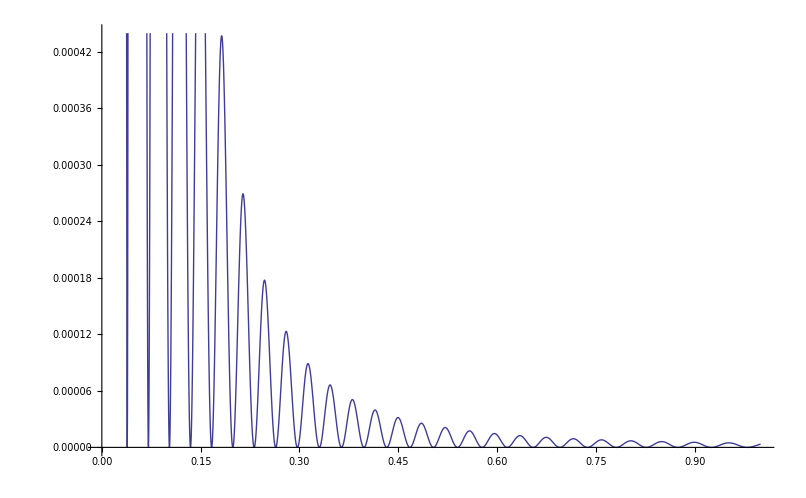

```mathematica
Plot[irr[t],{t,0,1}]
```

```mathematica
N[20*l/(2*Pi)]
```

2.01426×10^-6

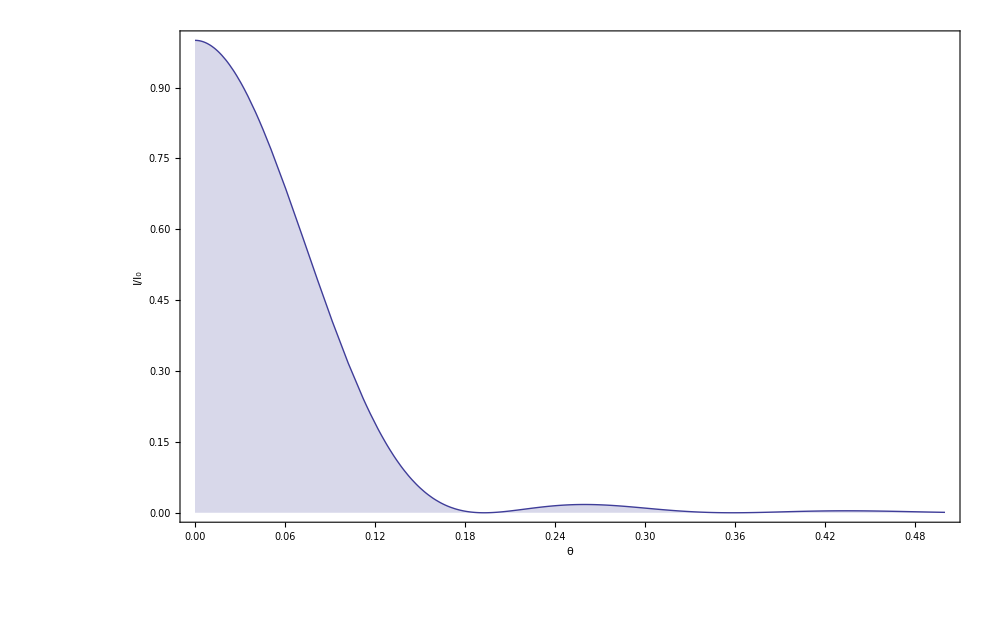

```mathematica
Plot[irr[t],{t,0,0.5},PlotRange->Full,FrameLabel-> {"θ","I/I_0"},Filling->Axis,Frame->True,TextStyle->{FontFamiy->"Helvetica",FontSize->25}]
```

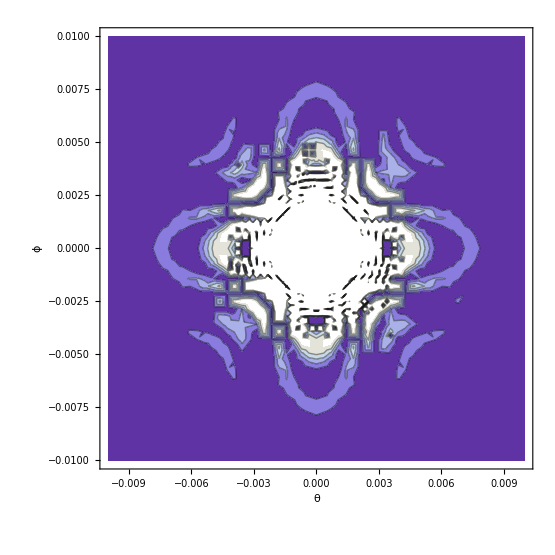

```mathematica
ContourPlot[irr2[r,q],{r,-0.01,0.01},{q,-0.01,0.01},FrameLabel-> {"θ","ϕ"},Frame->True,TextStyle->{FontFamiy->"Helvetica",FontSize->25},PerformanceGoal->"Quality"]
```

```mathematica
irr2[f_,s_]:=((2*BesselJ[1,20*Sin[Sqrt[f^2+s^2]]])/(20*Sin[Sqrt[f^2+s^2]]/l))^2
```

```mathematica
<<Graphics`Graphics`
```

General::obspkg: Graphics`Graphics` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Histogram::shdw: Symbol Histogram appears in multiple contexts Graphics`Graphics`System`; definitions in context Graphics`Graphics` may shadow or be shadowed by other definitions.

BarChart::shdw: Symbol BarChart appears in multiple contexts Graphics`Graphics`System`; definitions in context Graphics`Graphics` may shadow or be shadowed by other definitions.

BarSpacing::shdw: Symbol BarSpacing appears in multiple contexts Graphics`Graphics`System`; definitions in context Graphics`Graphics` may shadow or be shadowed by other definitions.

PieChart::shdw: Symbol PieChart appears in multiple contexts Graphics`Graphics`System`; definitions in context Graphics`Graphics` may shadow or be shadowed by other definitions.

```mathematica
DensityPlot[irr2[x,y],{x,-1,1},{y,-1,1},PlotPoints->200,WorkingPrecision->20,FrameLabel-> {"θ","ϕ"},Frame->True,TextStyle->{FontFamiy->"Helvetica",FontSize->25}]
```

-Graphics-

```mathematica
RevolutionPlot3D[irr[t],{t,0,1},{θ,0,Pi},PlotPoints->50]
```

-Graphics3D-

```mathematica
irr3[f_]:=(BesselJ[1,20*Sin[f]]/(20*Sin[f]))^2
```

```mathematica
N[3.832/Pi]
```

1.21976